```mathematica
length[x1_,y1_,x2_,y2_]:=√((x1-x2)^2+(y1-y2)^2)
length[2,3,8,11]
```

10

```mathematica
length[3,5,-1,-2]
```

√65

```mathematica
length2[x_,y_]:=√(x^2+y^2)
length2[-3,5]
```

√34

```mathematica
s=(a+b+c)/2;
trivojerkhetrofol[a_,b_,c_]:=Evaluate[√(s (s-a)(s-b)(s-c))]
trivojerkhetrofol[3,4,5]
```

6

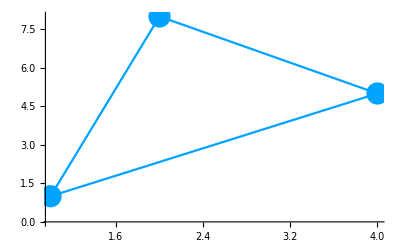

```mathematica
a={1,1};
b={4,5};
c={2,8};
plot1=ListPlot[{a,b,c},PlotStyle->{Hue[0.0],PointSize[0.04]}];
plot2=ListPlot[{a,c,b,a},PlotStyle->{Hue[0.56],PointSize[0.04]},Joined->True];
Show[p1,p2]
```